```mathematica
Quit[]
```

```mathematica
n=3
f[s_]=Sum[Subscript[a, i]/(i!)s^i,{i,0,2*n+1}]
df[s_]=D[f[s],s]
ddf[s_]=D[f[s],s,s]
dddf[s_]=D[f[s],s,s,s]

f[s]/.Solve[{f[-1]==0,f[1]==1},Table[Subscript[a, i],{i,0,2*n+1}]]
FullSimplify[%]
f[s]/.Solve[{f[-1]==0,f[1]==1,df[-1]==0,df[1]==0},Table[Subscript[a, i],{i,0,2*n+1}]]
FullSimplify[%]
f[s]/.Solve[{f[-1]==0,f[1]==1,df[-1]==0,df[1]==0,ddf[-1]==0,ddf[1]==0},Table[Subscript[a, i],{i,0,2*n+1}]]
FullSimplify[%]
f[s]/.Solve[{f[-1]==0,f[1]==1,df[-1]==0,df[1]==0,ddf[-1]==0,ddf[1]==0,dddf[-1]==0,dddf[1]==0},Table[Subscript[a, i],{i,0,2*n+1}]]
FullSimplify[%]
```

3

a_0+s a_1+(s^2 a_2)/2+(s^3 a_3)/6+(s^4 a_4)/24+(s^5 a_5)/120+(s^6 a_6)/720+(s^7 a_7)/5040

a_1+s a_2+(s^2 a_3)/2+(s^3 a_4)/6+(s^4 a_5)/24+(s^5 a_6)/120+(s^6 a_7)/720

a_2+s a_3+(s^2 a_4)/2+(s^3 a_5)/6+(s^4 a_6)/24+(s^5 a_7)/120

a_3+s a_4+(s^2 a_5)/2+(s^3 a_6)/6+(s^4 a_7)/24

{a_0+s a_1+(s^2 a_2)/2+(s^3 a_3)/6+1/720 s^6 (360-720 a_0-360 a_2-30 a_4)+(s^4 a_4)/24+(s^7 (2520-5040 a_1-840 a_3-42 a_5))/5040+(s^5 a_5)/120}

{-(-1+s^6) a_0+1/120 s (1+s) (60 s^5-(-1+s) (120 (1+s^2+s^4) a_1+20 (s+s^3) (3 a_2+s a_3)+5 s^3 a_4+s^4 a_5))}

{a_0+s a_1+1/24 s^4 (36-72 a_0-24 a_2)+(s^2 a_2)/2+1/720 s^6 (-720+1440 a_0+360 a_2)+1/120 s^5 (210-360 a_1-40 a_3)+(s^3 a_3)/6+(s^7 (-6300+10080 a_1+840 a_3))/5040}

{-1/4 s^4 (1+s)^2 (-6+5 s)+1/6 (-1+s^2)^2 (6 (1+2 s^2) a_0+s (6 (1+2 s^2) a_1+s (3 a_2+s a_3)))}

{1/720 s^6 (360-720 a_0)+1/2 s^2 (3-6 a_0)+a_0+1/24 s^4 (-36+72 a_0)+(s^7 (4725-5040 a_1))/5040+1/6 s^3 (105/8-18 a_1)+s a_1+1/120 s^5 (-315+360 a_1)}

{1/16 s^2 (1+s)^3 (24+s (-37+15 s))-(-1+s^2)^3 (a_0+s a_1)}

{1/2+(35 s)/32-(35 s^3)/32+(21 s^5)/32-(5 s^7)/32}

{1/32 (16+35 s-35 s^3+21 s^5-5 s^7)}

```mathematica
Table[2^-(2i),{i,1,4}]
```

{1/4,1/16,1/64,1/256}

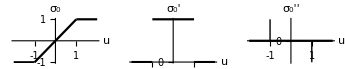

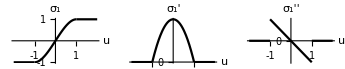

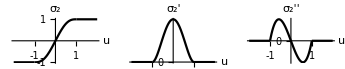

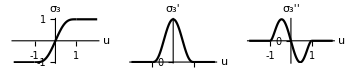

```mathematica
n=0;
f=s;
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])+UnitStep[s-1]]-UnitStep[-s-1];
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]'},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
p30=Plot[Evaluate[D[f,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]''},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
p31=Graphics[{Thick,Arrowheads[0],Arrow[{{1,0},{1,-1}}]}];
p32=Graphics[{Thick,Arrowheads[0],Arrow[{{-1,0},{-1,1}}]}];
p3=Show[p30,p31,p32];
g1=GraphicsGrid[{{p1,p2,p3}}]

n=1;
f=(3 s-s^3)/2;
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])+UnitStep[s-1]]-UnitStep[-s-1];
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]'},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
p3=Plot[Evaluate[D[f,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]''},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
g2=GraphicsGrid[{{p1,p2,p3}}]

n=2;
f=(15 s-10 s^3+3 s^5)/8;
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])+UnitStep[s-1]]-UnitStep[-s-1];
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]'},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
p3=Plot[Evaluate[D[f,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]''},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
g3=GraphicsGrid[{{p1,p2,p3}}]

n=3;
f=(35 s-35 s^3+21 s^5-5 s^7)/16;
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])+UnitStep[s-1]]-UnitStep[-s-1];
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]'},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
p3=Plot[Evaluate[D[f,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,Subscript[σ, n]''},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
g4=GraphicsGrid[{{p1,p2,p3}}]
```

```mathematica
-0
```

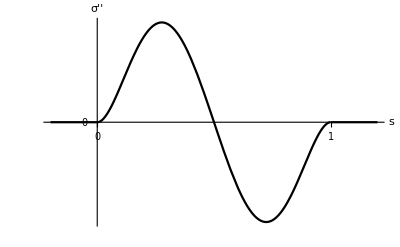

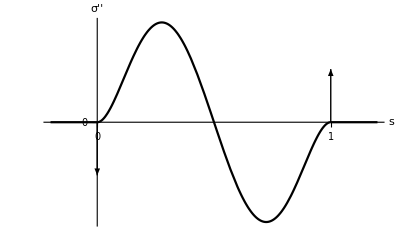

```mathematica
p3
p31=Graphics[{Thick,Arrowheads[.05],Arrow[{{1,0},{1,4}}]}];
p32=Graphics[{Thick,Arrowheads[.05],Arrow[{{0,0},{0,-4}}]}];
Show[p3,p31,p32]
```

```mathematica
Expand[(1+s)^3 (8+3 (-3+s) s)]
```

8+15 s-10 s^3+3 s^5

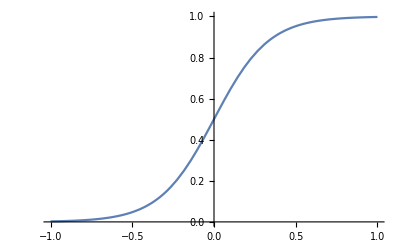

```mathematica
Plot[1/(1+Exp[-6*s]),{s,-1,1},PlotRange->{{-1,1},{0,1}}]
```

```mathematica
FullSimplify[1/(1+Exp[-6.0*s])/.s->-1]
```

0.00247262

```mathematica
Round[Log[10,0.001]]
10^N[%]
Round[Log[10,0.001]]
10^N[%]
```

-3

0.001

-3

0.001

```mathematica
2^-9.0
```

0.00195313

ⅇ^-s/((1+ⅇ^-s)^2)

(2 ⅇ^(-2 s))/((1+ⅇ^-s)^3)-ⅇ^-s/((1+ⅇ^-s)^2)

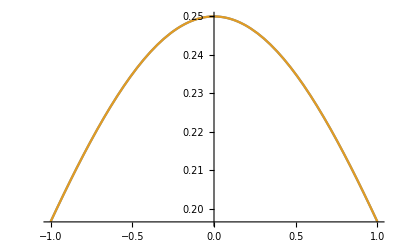

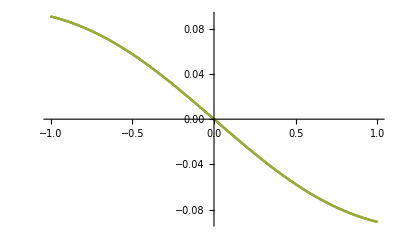

```mathematica
(*
f=(1+s)/2;
f=(2+3 s-s^3)/4;
f= (8+15 s-10 s^3+3 s^5)/16;
f=(16+35 s-35 s^3+21 s^5-5 s^7)/32;
*)
f=1/(1+Exp[-s]);
df=D[f,s]
ddf=D[df,s]
Plot[{df,f*(1-f)},{s,-1,1}]
Plot[{ddf,df*(1-f)-f*df,f(1-f)^2 -f^2(1-f)},{s,-1,1}]
```

```mathematica
n=2
f[s_]=Sum[Subscript[a, i]/(i!)s^i,{i,0,2*n+1}]
df[s_]=D[f[s],s]
ddf[s_]=D[f[s],s,s]
dddf[s_]=D[f[s],s,s,s]

f[s]/.Solve[{f[-1]==-1,f[1]==1},Table[Subscript[a, i],{i,0,2*n+1}]]
FullSimplify[%]
f[s]/.Solve[{f[-1]==-1,f[1]==1,df[-1]==0,df[1]==0},Table[Subscript[a, i],{i,0,2*n+1}]]
FullSimplify[%]
f[s]/.Solve[{f[-1]==-1,f[1]==1,df[-1]==0,df[1]==0,ddf[-1]==0,ddf[1]==0},Table[Subscript[a, i],{i,0,2*n+1}]]
FullSimplify[%]
f[s]/.Solve[{f[-1]==-1,f[1]==1,df[-1]==0,df[1]==0,ddf[-1]==0,ddf[1]==0,dddf[-1]==0,dddf[1]==0},Table[Subscript[a, i],{i,0,2*n+1}]]
FullSimplify[%]
```

2

a_0+s a_1+(s^2 a_2)/2+(s^3 a_3)/6+(s^4 a_4)/24+(s^5 a_5)/120

a_1+s a_2+(s^2 a_3)/2+(s^3 a_4)/6+(s^4 a_5)/24

a_2+s a_3+(s^2 a_4)/2+(s^3 a_5)/6

a_3+s a_4+(s^2 a_5)/2

Solve::svars: Equations may not give solutions for all "solve" variables.

{a_0+s a_1+1/24 s^4 (-24 a_0-12 a_2)+(s^2 a_2)/2+1/120 s^5 (120-120 a_1-20 a_3)+(s^3 a_3)/6}

{s^5-(-1+s^4) a_0-1/6 s (-1+s^2) (6 (1+s^2) a_1+s (3 a_2+s a_3))}

Solve::svars: Equations may not give solutions for all "solve" variables.

{a_0-2 s^2 a_0+s^4 a_0+1/6 s^3 (15-12 a_1)+s a_1+1/120 s^5 (-180+120 a_1)}

{1/2 s^3 (5-3 s^2)+(-1+s^2)^2 (a_0+s a_1)}

{(15 s)/8-(5 s^3)/4+(3 s^5)/8}

{1/8 s (15-10 s^2+3 s^4)}

a_0+s a_1+(s^2 a_2)/2+(s^3 a_3)/6+(s^4 a_4)/24+(s^5 a_5)/120

a_0+s a_1+1/120 s^2 (60 a_2+s (20 a_3+s (5 a_4+s a_5)))

```mathematica
Integrate[3s-s^3,s]
Integrate[15s-10s^3+3s^5,s]
Integrate[35s-35s^3+21s^5-5s^7,s]
```

(3 s^2)/2-s^4/4

(15 s^2)/2-(5 s^4)/2+s^6/2

(35 s^2)/2-(35 s^4)/4+(7 s^6)/2-(5 s^8)/8

```mathematica
1/2 s^2/.s->{-1,1}
(3 s^2)/2-s^4/4/.s->{-1,1}
(15 s^2)/2-(5 s^4)/2+s^6/2/.s->{-1,1}
(35 s^2)/2-(35 s^4)/4+(7 s^6)/2-(5 s^8)/8/.s->{-1,1}
```

{1/2,1/2}

{5/4,5/4}

{11/2,11/2}

{93/8,93/8}

```mathematica
D[1/2 s^2,s]/.s->{-1,1}
D[(3 s^2)/2-s^4/4,s]/.s->{-1,1}
D[(15 s^2)/2-(5 s^4)/2+(s^6/2).s]/.s->{-1,1}
D[(35 s^2)/2-(35 s^4)/4+(7 s^6)/2-(5 s^8)/8,s]/.s->{-1,1}
```

{-1,1}

{-2,2}

{5,5}

{-16,16}

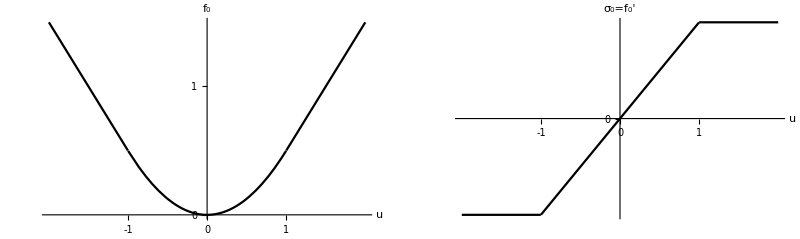

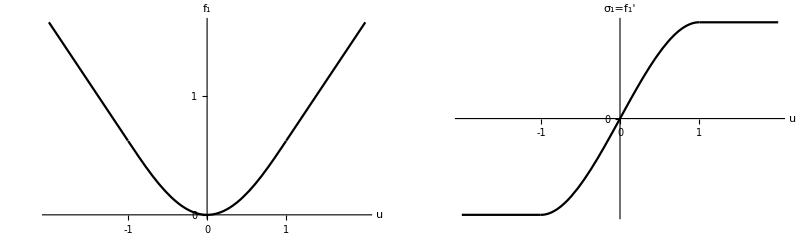

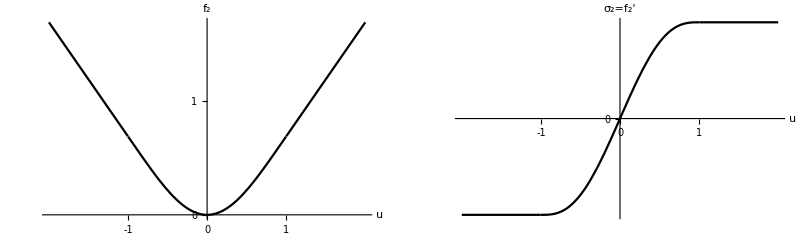

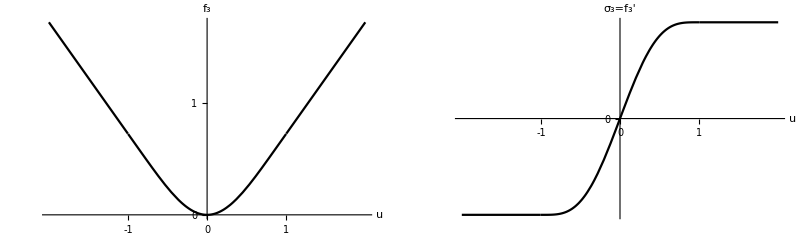

```mathematica
n=0;
f=1/2 s^2;
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])]+UnitStep[-s-1](-(s+1)+1/2)+UnitStep[s-1]((s-1)+1/2);
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"f_0"},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"σ_0=f_0'"},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
g1=GraphicsGrid[{{p1,p2}}]

n=1;
f=1/8(6 s^2-s^4);
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])]+UnitStep[-s-1](-(s+1)+5/8)+UnitStep[s-1]((s-1)+5/8);
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"f_1"},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"σ_1=f_1'"},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
g1=GraphicsGrid[{{p1,p2}}]

n=2;
f= 1/16(15 s^2-5 s^4+s^6);
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])]+UnitStep[-s-1](-(s+1)+11/16)+UnitStep[s-1]((s-1)+11/16);
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"f_2"},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"σ_2=f_2'"},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
g1=GraphicsGrid[{{p1,p2}}]

n=3;
f=1/128(140 s^2-70 s^4+28 s^6-5 s^8);
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])]+UnitStep[-s-1](-(s+1)+93/128)+UnitStep[s-1]((s-1)+93/128);
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"f_3"},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"σ_3=f_3'"},Ticks->{{-1,0,1},{0}},LabelStyle->Black];
g1=GraphicsGrid[{{p1,p2}}]
```

```mathematica
"0"
f=FullSimplify[2*(s)/2]
FullSimplify[D[f,s]]
"1"
f=FullSimplify[2*(3 s-s^3)/4]
FullSimplify[D[f,s]]
"2"
f=FullSimplify[ 2*(15 s-10 s^3+3 s^5)/16]
FullSimplify[D[f,s]]
"3"
f=FullSimplify[2*(35 s-35 s^3+21 s^5-5 s^7)/32]
FullSimplify[D[f,s]]
```

0

s

1

1

-1/2 s (-3+s^2)

-3/2 (-1+s^2)

2

1/8 s (15-10 s^2+3 s^4)

15/8 (-1+s^2)^2

3

1/16 (35 s-35 s^3+21 s^5-5 s^7)

-35/16 (-1+s^2)^3

```mathematica
n=0;
f=s;
FullSimplify[f]
"------------------------------------------"
n=1;
f=(3 s-s^3)/2;
FullSimplify[f]
"------------------------------------------"
n=2;
f=(15 s-10 s^3+3 s^5)/8;
FullSimplify[f]
"------------------------------------------"
n=3;
f=(35 s-35 s^3+21 s^5-5 s^7)/16;
FullSimplify[f]
"------------------------------------------"
```

s

------------------------------------------

-1/2 s (-3+s^2)

------------------------------------------

1/8 s (15-10 s^2+3 s^4)

------------------------------------------

1/16 (35 s-35 s^3+21 s^5-5 s^7)

------------------------------------------

```mathematica
n=0;
f=s;
g=FullSimplify[Integrate[f,s]]
g/.s->1
D[g,s]/.s->1
Expand[2*g]
"------------------------------------------"
n=1;
f=(3 s-s^3)/2;
g=FullSimplify[Integrate[f,s]]
g/.s->1
D[g,s]/.s->1
Expand[8*g]
"------------------------------------------"
n=2;
f=(15 s-10 s^3+3 s^5)/8;
g=FullSimplify[Integrate[f,s]]
g/.s->1
D[g,s]/.s->1
Expand[16*g]
"------------------------------------------"
n=3;
f=(35 s-35 s^3+21 s^5-5 s^7)/16;
g=FullSimplify[Integrate[f,s]]
g/.s->1
D[g,s]/.s->1
Expand[128*g]
"------------------------------------------"
```

s^2/2

1/2

1

s^2

------------------------------------------

-1/8 s^2 (-6+s^2)

5/8

1

6 s^2-s^4

------------------------------------------

1/16 s^2 (15-5 s^2+s^4)

11/16

1

15 s^2-5 s^4+s^6

------------------------------------------

1/128 (140 s^2-70 s^4+28 s^6-5 s^8)

93/128

1

140 s^2-70 s^4+28 s^6-5 s^8

------------------------------------------

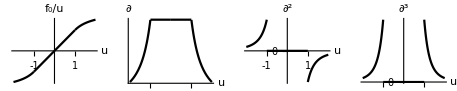

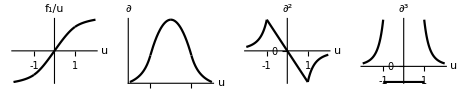

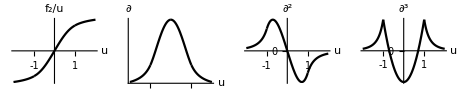

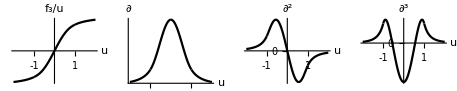

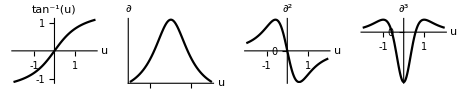

```mathematica
n=0;
f=1/2 s^2;
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])]+UnitStep[-s-1](-(s+1)+1/2)+UnitStep[s-1]((s-1)+1/2);
f=Evaluate[f/s];
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"f_0/u"},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂"},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p3=Plot[Evaluate[D[f,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂^2 "},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p4=Plot[Evaluate[D[f,s,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂^3 "},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
g1=GraphicsGrid[{{p1,p2,p3,p4}}]

n=1;
f=1/8(6 s^2-s^4);
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])]+UnitStep[-s-1](-(s+1)+5/8)+UnitStep[s-1]((s-1)+5/8);
f=Evaluate[f/s];
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"f_1/u"},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂"},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p3=Plot[Evaluate[D[f,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂^2 "},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p4=Plot[Evaluate[D[f,s,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂^3 "},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
g1=GraphicsGrid[{{p1,p2,p3,p4}}]

n=2;
f= 1/16(15 s^2-5 s^4+s^6);
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])]+UnitStep[-s-1](-(s+1)+11/16)+UnitStep[s-1]((s-1)+11/16);
f=Evaluate[f/s];
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"f_2/u"},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂"},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p3=Plot[Evaluate[D[f,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂^2 "},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p4=Plot[Evaluate[D[f,s,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂^3 "},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
g1=GraphicsGrid[{{p1,p2,p3,p4}}]

n=3;
f=1/128(140 s^2-70 s^4+28 s^6-5 s^8);
f=Evaluate[f*(UnitStep[s+1]-UnitStep[s-1])]+UnitStep[-s-1](-(s+1)+93/128)+UnitStep[s-1]((s-1)+93/128);
f=Evaluate[f/s];
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"f_3/u"},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂"},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p3=Plot[Evaluate[D[f,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂^2 "},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p4=Plot[Evaluate[D[f,s,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂^3 "},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
g1=GraphicsGrid[{{p1,p2,p3,p4}}]

f=ArcTan[s];
p1=Plot[f,{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{"u","tan^-1(u)"},Ticks->{{-1,0,1},{-1,0,1}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p2=Plot[Evaluate[D[f,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂"},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p3=Plot[Evaluate[D[f,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂^2 "},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
p4=Plot[Evaluate[D[f,s,s,s]],{s,-2,2},PlotStyle->{Bold,Black},AxesLabel->{u,"∂^3 "},Ticks->{{-1,0,1},{0}},LabelStyle->Black,PlotRange->All,AxesOrigin->{0,0}];
g1=GraphicsGrid[{{p1,p2,p3,p4}}]
```

```mathematica
+UnitStep[-s-1](-(s+1)+2)+UnitStep[s-1]((s-1)+11/16)
```

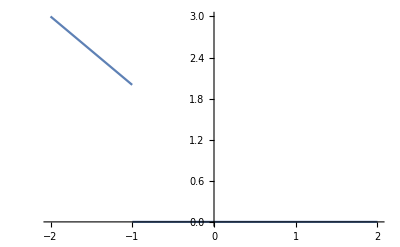

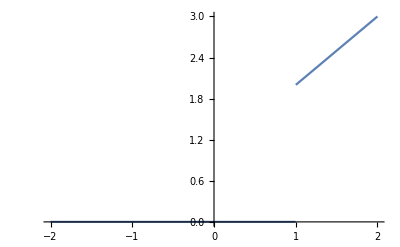

```mathematica
Plot[UnitStep[-s-1](-(s+1)+2),{s,-2,2}]
Plot[UnitStep[s-1]((s-1)+2),{s,-2,2}]
```

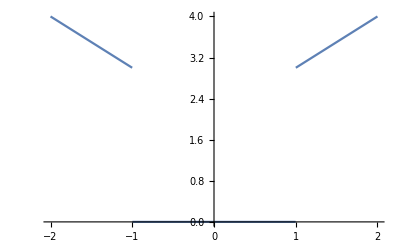

```mathematica
Plot[UnitStep[Sign[s]s-1](3-1+Sign[s]*s),{s,-2,2}]
```

Tanh[u]

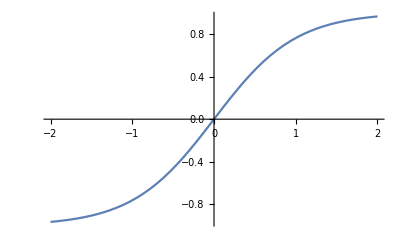

Log[Cosh[u]]

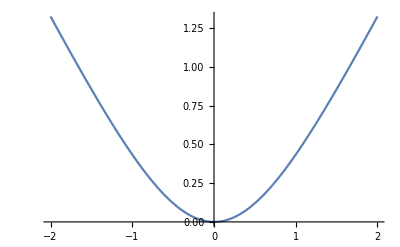

Sech[u]^2

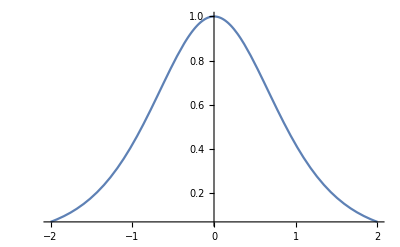

-2 Sech[u]^2 Tanh[u]

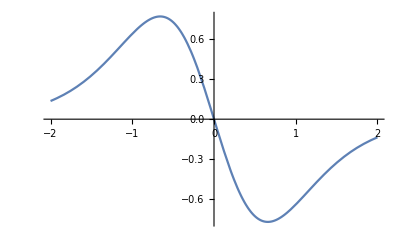

2 (-2+Cosh[2 u]) Sech[u]^4

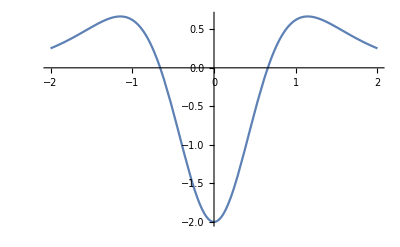

```mathematica
sig=FullSimplify[2/(1+Exp[-2*u])-1]
Plot[Evaluate[sig/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[Integrate[sig,u]];
FullSimplify[%-(%/.u->0)]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u]]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u,u]]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u,u,u]]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
```

ArcTan[u]

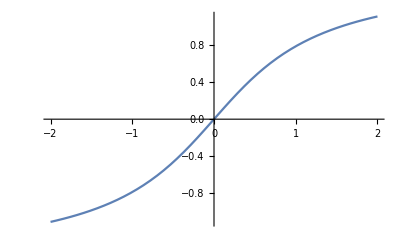

u ArcTan[u]-1/2 Log[1+u^2]

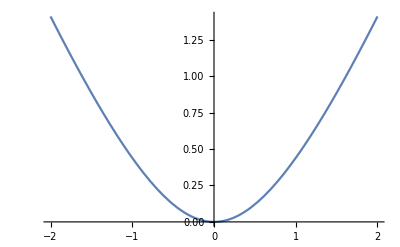

1/(1+u^2)

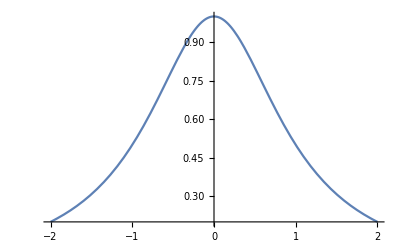

-(2 u)/((1+u^2)^2)

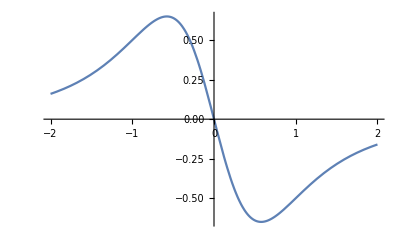

(-2+6 u^2)/((1+u^2)^3)

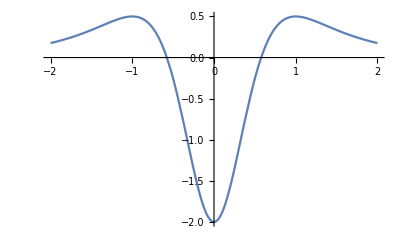

```mathematica
sig=FullSimplify[ArcTan[u]]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[Integrate[sig,u]];
FullSimplify[%-(%/.u->0)]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u]]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u,u]]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u,u,u]]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
```

If[Abs[u]<t,0,Sign[u]-t/u]

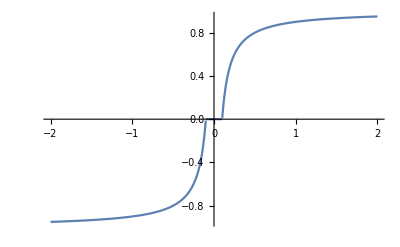

Integrate::ilim: Invalid integration variable or limit(s) in 0.

∫If[Abs[u]<t,0,Sign[u]-t/u]ⅆu-∫(Piecewise[{{ComplexInfinity, t≤0}, {0, True}}])ⅆ0

Integrate::ilim: Invalid integration variable or limit(s) in 0.

Integrate::ilim: Invalid integration variable or limit(s) in -1.99992.

Integrate::ilim: Invalid integration variable or limit(s) in -1.91829.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

-Graphics-

If[Abs[u]<t,0,t/u^2+Sign'[u]]

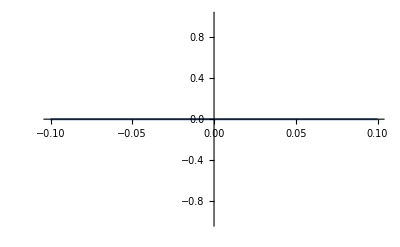

If[Abs[u]<t,0,-(2 t)/u^3+(Sign')'[u]]

-Graphics-

Piecewise[{{(6 t)/u^4+Sign^(3)[u], t≤Abs[u]}, {0, True}}]

-Graphics-

```mathematica
sig=FullSimplify[If[Abs[u]<t,0,Sign[u]-t/u]]
Plot[Evaluate[%/.t->.1],{u,-2,2},PlotRange->All]
FullSimplify[Integrate[sig,u]];
FullSimplify[%-(%/.u->0)]/.Sign'[u]->0
Plot[Evaluate[%/.t->.1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u]]/.(Sign')'[u]->0
Plot[Evaluate[%/.t->.1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u,u]]/.(Sign')'[u]->0
Plot[Evaluate[%/.t->.1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u,u,u]]/.Sign'[u]->0
Plot[Evaluate[%/.t->.1],{u,-2,2},PlotRange->All]
```

```mathematica
Quit[]
```

Log[Cosh[u]]/u

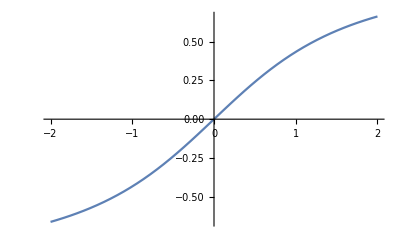

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Integrate::ilim: Invalid integration variable or limit(s) in 0.

-∫Indeterminateⅆ0+∫Log[Cosh[u]]/u ⅆu

Integrate::ilim: Invalid integration variable or limit(s) in -1.99992.

Integrate::ilim: Invalid integration variable or limit(s) in -1.91829.

Integrate::ilim: Invalid integration variable or limit(s) in -1.83665.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

-Graphics-

(-Log[Cosh[u]]+u Tanh[u])/u^2

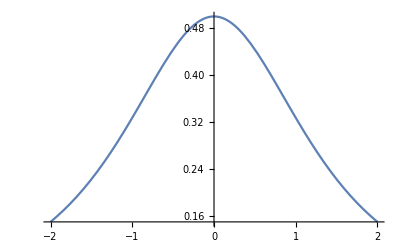

(2 Log[Cosh[u]]+u^2 Sech[u]^2-2 u Tanh[u])/u^3

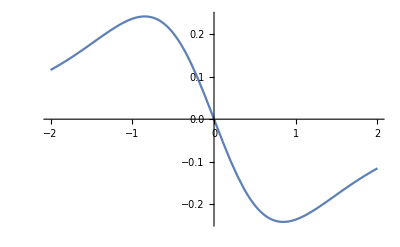

(-6 Log[Cosh[u]]+6 u Tanh[u]-u^2 Sech[u]^2 (3+2 u Tanh[u]))/u^4

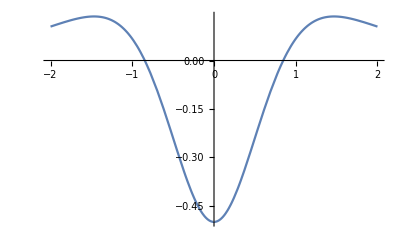

```mathematica
sig=FullSimplify[FullSimplify[Integrate[Tanh[u],u]]/u]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[Integrate[sig,u]];
FullSimplify[%-(%/.u->0)]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u]]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u,u]]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
FullSimplify[D[sig,u,u,u]]
Plot[Evaluate[%/.t->1],{u,-2,2},PlotRange->All]
```

```mathematica
-1+(140/2-70/4+28/6-5/8)/128
```

-1715/3072

```mathematica
(93/128-1)
```

-35/128

```mathematica
140/2
```

70

```mathematica
70/4
```

35/2

```mathematica
28/6
```

14/3

```mathematica
70/128
```

35/64

```mathematica
(93/128-1)
```

```mathematica
(140/2-70/4+28/6-5/8)/128
```

1357/3072

```mathematica
93/128-1
```

-35/128

```mathematica
(93/128-1)
```

-35/128

```mathematica
3*70
```

210

```mathematica
5*28
```

140

```mathematica
7*5
```

35

```mathematica
FullSimplify[(-2*3*70+3*4*5*28*u^2-5*6*7*5*u^4)/128]
```

-105/64 (2-8 u^2+5 u^4)

```mathematica
93/128-1
```

-35/128

```mathematica
(93/128-1)
```

-35/128

```mathematica
-(93/128-1)
```

35/128

```mathematica
2*(93/128-1)/u^3
```

-35/(64 u^3)

```mathematica
-6*(93/128-1)/u^4
```

105/(64 u^4)

Piecewise[{{x/(2-2 x), x<0}, {x/(2+2 x), True}}]

Piecewise[{{-x/2-1/2 Log[1-x], x≤0}, {1/2 (x-Log[1+x]), True}}]

1

Piecewise[{{1/(2 (-1+x)^2), x≤0}, {1/(2 (1+x)^2), True}}]

2

Piecewise[{{-1/(-1+x)^3, x<0}, {-1/(1+x)^3, x>0}, {Indeterminate, True}}]

3

Piecewise[{{3/(-1+x)^4, x<0}, {3/(1+x)^4, x>0}, {Indeterminate, True}}]

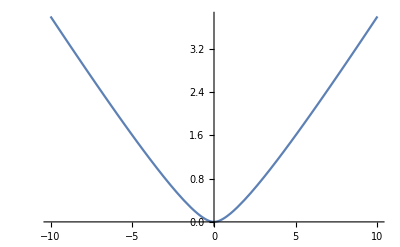

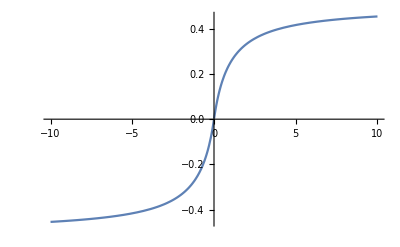

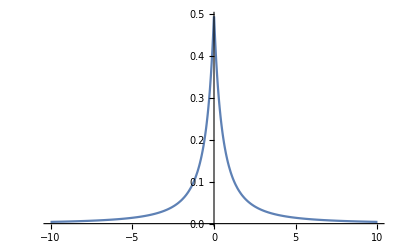

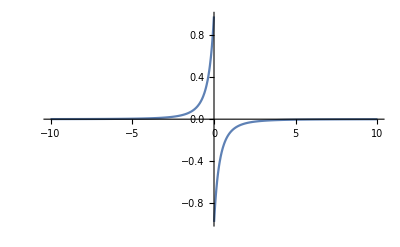

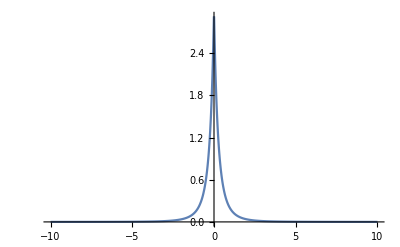

```mathematica
y =FullSimplify[If[x<0,Sign[x-1]-1/(x-1)/2+1/2,Sign[x+1]-1/(x+1)/2-1/2]]
Y=Evaluate[Integrate[y,x]];
Y=FullSimplify[Evaluate[Y-(Y/.x->0)]]
1
Dy=FullSimplify[D[y,x]]
2
DDy=FullSimplify[D[Dy,x]]
3
DDDy=FullSimplify[D[DDy,x]]
Plot[Y,{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
Plot[y,{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
Plot[Dy,{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
Plot[DDy,{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
Plot[DDDy,{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Quit[]
```

(1-Log[2]/Log[2+Abs[x]]) Sign[x]

Integrate::ilim: Invalid integration variable or limit(s) in 0.

-∫0ⅆ0+∫(1-Log[2]/Log[2+Abs[x]]) Sign[x]ⅆx

Sign'[x]+(Log[2] ((Sign[x] Abs'[x])/(2+Abs[x])-Log[2+Abs[x]] Sign'[x]))/Log[2+Abs[x]]^2

(Log[4] Abs'[x] (-Sign[x] Abs'[x]+(2+Abs[x]) Log[2+Abs[x]] Sign'[x]))/((2+Abs[x])^2 Log[2+Abs[x]]^3)+Sign''[x]+(Log[2] ((Sign[x] (-Abs'[x]^2+(2+Abs[x]) Abs''[x]))/(2+Abs[x])^2-Log[2+Abs[x]] Sign''[x]))/Log[2+Abs[x]]^2

(Log[2] Sign[x] (2 (3+Log[2+Abs[x]] (3+Log[2+Abs[x]])) Abs'[x]^3-3 (2+Abs[x]) Log[2+Abs[x]] (2+Log[2+Abs[x]]) Abs'[x] Abs''[x]+(2+Abs[x])^2 Log[2+Abs[x]]^2 Abs^(3)[x])+(2+Abs[x]) Log[2+Abs[x]] (-3 Log[2] (2+Log[2+Abs[x]]) Abs'[x]^2 Sign'[x]+(2+Abs[x]) Log[8] Log[2+Abs[x]] Abs'[x] Sign''[x]+(2+Abs[x]) Log[2+Abs[x]] (Log[8] Sign'[x] Abs''[x]-(2+Abs[x]) Log[2/(2+Abs[x])] Log[2+Abs[x]] Sign^(3)[x])))/((2+Abs[x])^3 Log[2+Abs[x]]^4)

Integrate::ilim: Invalid integration variable or limit(s) in -9.99959.

Integrate::ilim: Invalid integration variable or limit(s) in -9.59143.

Integrate::ilim: Invalid integration variable or limit(s) in -9.18326.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

-Graphics-

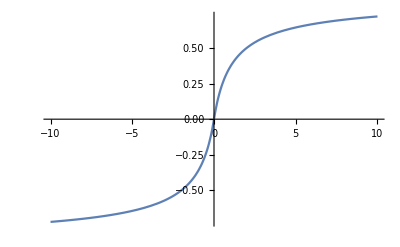

-Graphics-

-Graphics-

-Graphics-

```mathematica
y =FullSimplify[Sign[x]*(-Log[2]/Log[2+Abs[x]]+1)]
Y=Evaluate[Integrate[y,x]];
Y=FullSimplify[Evaluate[Y-(Y/.x->0)]]
Dy=FullSimplify[D[y,x]]
DDy=FullSimplify[D[Dy,x]]
DDDy=FullSimplify[D[DDy,x]]
Plot[Y,{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
Plot[y,{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
Plot[Dy,{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
Plot[DDy,{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
Plot[DDDy,{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
y=-(Log[2] (2+Log[2+Abs[u]]))/((2+Abs[u])^2 Log[2+Abs[u]]^3);
FullSimplify[D[y,u]]
```

(Log[4] (3+Log[2+Abs[u]] (3+Log[2+Abs[u]])) Abs'[u])/((2+Abs[u])^3 Log[2+Abs[u]]^4)

(ⅇ^(-x^2))/(√π)+x Erf[x]

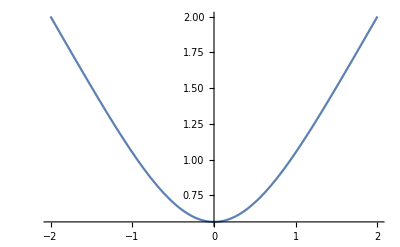

```mathematica
Integrate[Erf[x],x]
Plot[%,{x,-2,2}]
```

```mathematica
(ⅇ^(-x^2))/(√π)+x Erf[x]/.x->0
```

1/(√π)

```mathematica
FullSimplify[Integrate[u-u^3+(3 u^5)/5-u^7/7,u]]
```

1/280 u^2 (140-70 u^2+28 u^4-5 u^6)

```mathematica
u-u^3+(3*u^5)/5-u^7/7/.u->1
```

16/35

```mathematica
1/280/93*280
```

1/93

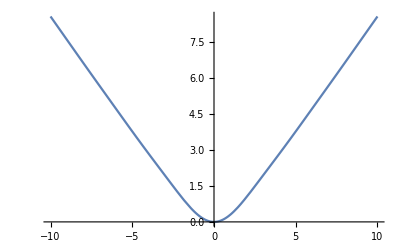

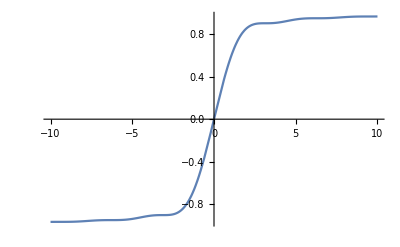

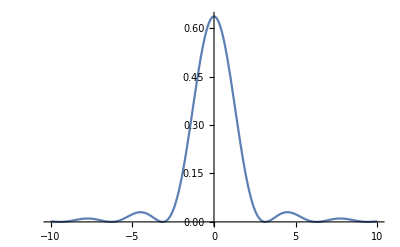

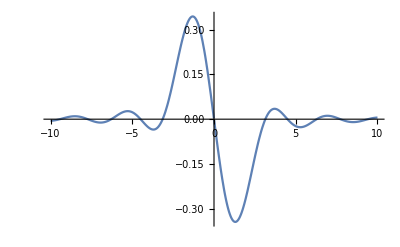

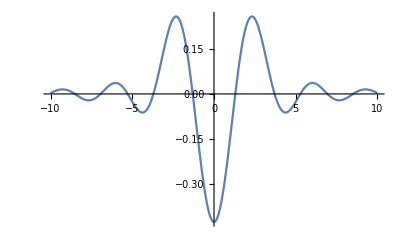

(-1-EulerGamma+Cos[2 x]+CosIntegral[2 x]-Log[2 x]+2 x SinIntegral[2 x])/π

(-1+Cos[2 x]+2 x SinIntegral[2 x])/(π x)

(2 Sinc[x]^2)/π

(4 (x Cos[x]-Sin[x]) Sinc[x])/(π x^2)

(6+(-6+4 x^2) Cos[2 x]-8 x Sin[2 x])/(π x^4)

```mathematica
Dy=FullSimplify[Sinc[x]^2*2/Pi];
DDy =FullSimplify[D[Dy,x]];
DDDy = FullSimplify[D[DDy,x]];
y=FullSimplify[Integrate[Dy,x]];
Y=FullSimplify[Integrate[y,x]];
Y=FullSimplify[Evaluate[Y-Limit[Y,x->0]]];
Plot[Y,{x,-10,10},PlotRange->All,AxesOrigin->{0,0}]
Plot[y,{x,-10,10},PlotRange->All,PlotRange->All,AxesOrigin->{0,0}]
Plot[Dy,{x,-10,10},PlotRange->All,PlotRange->All,AxesOrigin->{0,0}]
Plot[DDy,{x,-10,10},PlotRange->All,PlotRange->All,AxesOrigin->{0,0}]
Plot[DDDy,{x,-10,10},PlotRange->All,PlotRange->All,AxesOrigin->{0,0}]
Y
y
Dy
DDy
DDDy
```

```mathematica
Quit[]
```

0.1

1

Piecewise[{{-1+(1-x/p)^-p, x<0}, {1-((p+x)/p)^-p, True}}]

-p/(-1+p)+(Piecewise[{{-x+((p-x) (1-x/p)^-p)/(-1+p), x≤0}, {x+((p+x) ((p+x)/p)^-p)/(-1+p), True}}])

Piecewise[{{((p+x)/p)^(-1-p), x≥0}, {(p (1-x/p)^-p)/(p-x), True}}]

Piecewise[{{-(p (1+p) ((p+x)/p)^-p)/(p+x)^2, x>0}, {(p (1+p) (1-x/p)^-p)/(p-x)^2, x<0}, {Indeterminate, True}}]

Piecewise[{{(p (1+p) (2+p) ((p+x)/p)^-p)/(p+x)^3, x>0}, {(p (1+p) (2+p) (1-x/p)^-p)/(p-x)^3, x<0}, {Indeterminate, True}}]

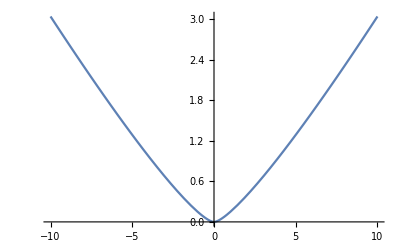

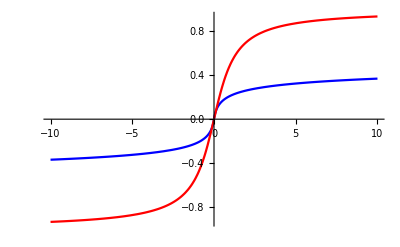

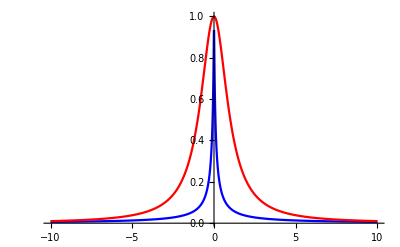

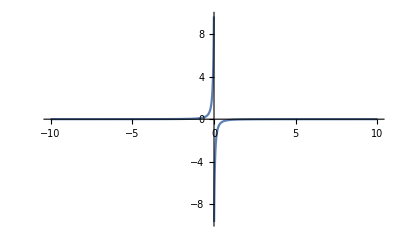

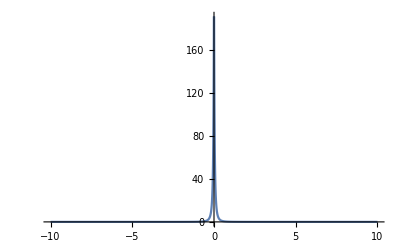

```mathematica
q=0.1
t=1
y =FullSimplify[If[x<0,-1+1/(-x/p+1)^p,1-1/(x/p+1)^p]]
Y=Evaluate[Integrate[y,x]];
Y=FullSimplify[Evaluate[Y-(Y/.x->0)]]
Dy=FullSimplify[D[y,x]]
DDy=FullSimplify[D[Dy,x]]
DDDy=FullSimplify[D[DDy,x]]
Plot[Evaluate[Y/.s->t/.p->q],{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
Plot[{Evaluate[y/.s->t/.p->q],ArcTan[x]/(Pi/2)},{x,-10,10},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Blue,Red}]
Plot[{Evaluate[Dy/.s->t/.p->q],1/(1+x^2)},{x,-10,10},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Blue,Red}]
Plot[Evaluate[DDy/.s->t/.p->q],{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
Plot[Evaluate[DDDy/.s->t/.p->q],{x,-10,10},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Quit[]
```

```mathematica
Solve[Evaluate[1-1/(s*x+1)^p/.x->1 ]== 0.9,s]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s→0.1^(-1./p) (1.-1. 0.1^(1/p))}}

```mathematica
(((p+x)/p)^(-1-p)==D[ArcTan[x],x])/.x->0
```

True

```mathematica
(p (1+p) (2+p) ((p+x)/p)^-p)/(p+x)^3/.x->0
```

((1+p) (2+p))/p^2